# Existence and Stability of Static Fluid Shells in a Schwarzschild-Rindler-anti-de Sitter Metric - G. Alestas, G. V. Kraniotis and L. Perivolaropoulos

## General Settings

### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
(* Some unimportant error messages are switched off for future convenience *)
Off[Power::infy,FindRoot::lstol, Infinity::indet];
```

### PlotGrid Module

```mathematica
(*Neccesary for the creation of figure 1*)
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]

fillVertical[plot_,x0_: -0.12]:=plot/.Line[p_]:>{{Opacity[0.2],Polygon[p~Join~{{N@x0,p[[-1,2]]},{N@x0,p[[1,2]]}}]},Line[p]}
```

## III. Special Cases

### III.1. Vacuum Fluid Shell (w = -1)

#### Figure 1

```mathematica
Clear[m1,m2,ss,b,ll,s1,r1];
m1r=m1 - b r^2 +ll r^3 /6;
m2r=m2 - b r^2 +ll r^3 /6;
msr= 4 Pi ss r^2;
vv=1+(4 m1r m2r)/msr^2-(msr/(2 r) + (m1r+m2r)/(msr))^2;
vv1=FullSimplify[vv];
vvp=D[vv1,r] //Expand;
eq1=vv1==0;
eq2=vvp==0;
vvpp=D[vv1,{r,2}];
sol1=Solve[eq1 &&eq2  &&vvpp>0 && m1>0 && m2>0 && r>0  && ss>0,  {ll,b},{Reals}]//FullSimplify;
lr[r_,ss_]:=(6 (m1+m2)-3 r)/r^3+(15 (m1-m2)^2)/(16 π^2 r^6 ss^2)-12 π^2 ss^2; 
r0:=  3 (m1+m2)+r1;(*Minimum value of r*)
s0[r_]:=(√15 √(-(m1-m2)^2/((3 (m1+m2)-r) r^3)))/(4 π)+s1; (*Minimum value of σ, written as a function of r*)
br[r_,ss_]:=(8 (3 (m1+m2)-2 r) r^3+(3 (m1-m2)^2)/(π^2 ss^2))/(16 r^5);
lr[r0,s0[r0]]//FullSimplify;
br[r0,s0[r0]]//FullSimplify;
```

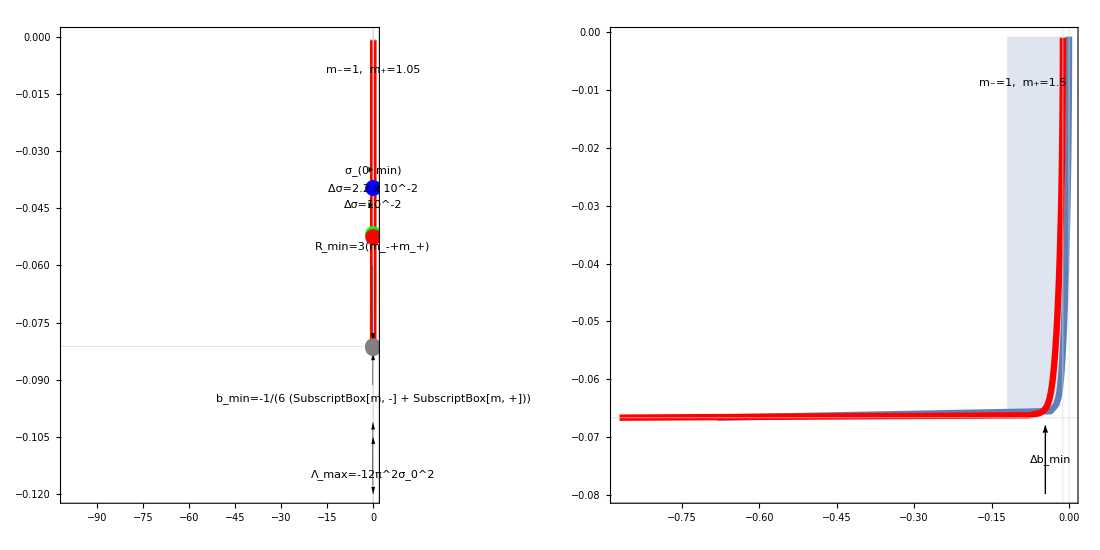
-Graphics-Λb

```mathematica
(*It is used to join multiple plots together with a common axis "ALWAYS RUN FIRST!!"*)

m1=1;
m2=1.05;
bmin1=-1/(6(m1+m2));
Clear[s1]
s1=0;
lmin1=-12 Pi^2 s0[r]^2 /. r->500;
pl1=ParametricPlot[{lr[r0,s0[r0]],br[r0,s0[r0]]},{r1,0.01,1000},Frame->True,AspectRatio->1,PlotStyle->Thickness[0.008]];
Clear[s1]
s1=0.022;
lmin2=-12 Pi^2 s0[r]^2 /. r->500;
pl2=ParametricPlot[{lr[r0,s0[r0]],br[r0,s0[r0]]},{r1,0.01,1000},Frame->True,AspectRatio->1,PlotRange->All,PlotStyle->{Thickness[0.008],Yellow}];
pl3=ListLinePlot[{{-100,bmin1},{lmin2,bmin1}},Filling->{1->{Top,Transparent}},PlotStyle->{Transparent, Thickness[0.008],Dashed},Frame->True,AspectRatio->1,PlotRange->All,Axes->False];
pl4=ListLinePlot[{{-100,bmin1},{lmin1,bmin1}},PlotStyle->{Transparent, Thickness[0.008],Dashed},Frame->True,AspectRatio->1,PlotRange->All,Axes->False];
Clear[s1]
s1=0.01;
lmin3=-12 Pi^2 s0[r]^2 /. r->500;
pl5=ParametricPlot[{lr[r0,s0[r0]],br[r0,s0[r0]]},{r1,0.01,1000},Frame->True,AspectRatio->1,PlotRange->All,PlotStyle->{Thickness[0.008],Red}];
s1=0.001;

pl6=fillVertical[pl1];

fig[1]=Show[pl6,pl2,pl3,pl4,pl5,Graphics[{Inset[Framed["m_-=1,  m_+=1.05"],{-0.09,-0.008737}]}],Graphics[{Inset["b_min=-1/(6 (SubscriptBox[m, -] + SubscriptBox[m, +]))",{-0.09,-0.095}]}],Graphics[{Inset["Λ_max=-12π^2σ_0^2",{-0.09,-0.115}]}],Graphics[{Inset["Δσ=10^-2",{-0.042,-0.04415}]}],Graphics[{Inset["Δσ=2.2 x 10^-2",{-0.095,-0.04}]}],Graphics[{Inset["σ_(0  min)",{-0.0392,-0.035}]}],Graphics[{Inset["R_min=3(m_-+m_+)",{-0.095,-0.05519}]}],Graphics[Arrow[{{-0.07193,-0.09137},{-0.063,-0.083}}]],Graphics[Arrow[{{-0.07024,-0.1153},{-0.01226,-0.105}}]],Graphics[Arrow[{{-0.07024,-0.1153}, {-0.001202,-0.12}}]],Graphics[Arrow[{{-0.07024,-0.1153}, {-0.05816,-0.1012}}]],
Graphics[Arrow[{{-0.03143,-0.04415}, {-0.01962,-0.04415}}]],Graphics[Arrow[{{-0.0321,-0.03489}, {-0.0061,-0.03489}}]],Graphics[Arrow[{{-0.07812,-0.04045}, {-0.06396,-0.04045}}]],Graphics[Arrow[{{-0.0944,-0.06011}, {-0.07523,-0.0797}}]],Graphics[Arrow[{{-0.0944,-0.06011}, {-0.04226,-0.0797}}]],GridLines->{{lmin1,lmin2,lmin3}, {bmin1}},GridLinesStyle->{{Green, Thickness[0.008],Dashed},{Orange, Thickness[0.008],Dashed}},BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->16],ImageSize->Large,Axes->False,PlotRange->{{0.005,-0.11},{0,-0.12}},Filling-> {3-> {Axis,LightRed}},Epilog->{{Gray,PointSize[0.02],Point[{-0.07403,-0.08121}]},{Blue,PointSize[0.02],Point[{-0.01722,-0.0397}]},{Gray,PointSize[0.02],Point[{-0.03913,-0.08171}]},{Green,PointSize[0.02],Point[{-0.06705,-0.05182}]},{Red,PointSize[0.02],Point[{-0.006393,-0.05258}]}}];

arrow=Graphics[{FilledCurve[{Line[{{-1.5,0.},{-1.5,0.},{-1.95,1.05},{0.,0.},{0.,-1.05},{0.15,-1.05},{0.15,1.05},{0.,1.05},{0.,0.},{-1.95,-1.05},{-1.5,0.}}]}]}];

m1=1;
m2=1.5;
bmin2=-1/(6(m1+m2));
Clear[s1]
s1=0;
lmin1=-12 Pi^2 s0[r]^2 /. r->500;
pl1=ParametricPlot[{lr[r0,s0[r0]],br[r0,s0[r0]]},{r1,0.01,1000},Frame->True,AspectRatio->1,PlotStyle->Thickness[0.008]];
Clear[s1]
s1=0.01;
lmin2=-12 Pi^2 s0[r]^2 /. r->500;
pl2=ParametricPlot[{lr[r0,s0[r0]],br[r0,s0[r0]]},{r1,0.01,1000},Frame->True,AspectRatio->1,PlotRange->All,PlotStyle->{Thickness[0.008],Red}];
pl3=ListLinePlot[{{-100,bmin2},{lmin2,bmin2}},Filling->{1->{Top,Transparent}},PlotStyle->{Transparent, Thickness[0.008],Dashed},Frame->True,AspectRatio->1,PlotRange->All,Axes->False];
pl4=ListLinePlot[{{-100,bmin2},{lmin1,bmin2}},PlotStyle->{Transparent, Thickness[0.008],Dashed},Frame->True,AspectRatio->1,PlotRange->All,Axes->False];
plt=fillVertical[pl1];
fig[2]=Show[plt,pl2,Graphics[{Inset[Framed["m_-=1,  m_+=1.5"],{-0.09,-0.008737}]}],Graphics[{Inset["Δb_min",{-0.0365,-0.07392}]}],Graphics[Arrowheads[{{0.01,1,arrow},{-0.01,0,arrow}}]],Graphics[Arrow[{{-0.04585,-0.07985}, {-0.04585,-0.068}}]],GridLines->{{lmin1,lmin2}, {bmin1,bmin2}},GridLinesStyle->{{Green, Thickness[0.008],Dashed},{Orange, Thickness[0.008],Dashed}},BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->16],ImageSize->Large,Axes->False,PlotRange->{{0.005,-0.11},{0,-0.12}},Filling-> {2-> {{1},Transparent}},Method->{"GridLinesInFront"->True}];

grid1=Table[fig[i],{m,1},{i,1,2}];

k1=Panel[plotGrid[grid1,1100,550],{"Λ",Rotate["b",Pi/2]},{Bottom,Left},Background->White]
```

```mathematica
Export["figure1.pdf",k1,ImageResolution->1000,ImageSize->Scaled[4]]
```

```mathematica
Quit[]
```

#### Figure 2

```mathematica
Clear[m1,m2,s0,s1,b,ll,r1,rmin,vv];
m1=1;
m2=1.05;
rmin=3(m1+m2);
r[r1_]:=rmin+r1;
m1r[r1_]:=m1 - b r[r1]^2 +ll r[r1]^3 /6;
m2r[r1_]:=m2 - b r[r1]^2 +ll r[r1]^3 /6;
s1=0.001;
s0[r1_]:=(√15 √(-(m1-m2)^2/((3 (m1+m2)-r[1]) r[r1]^3)))/(4 π)-s1;
msr[r1_]:= 4 Pi s0[r1](rmin+r1)^2;
vv[r1_]=1+(4 m1r[r1]*m2r[r1])/msr[r1]^2-(msr[r1]/(2 r[r1]) + (m1r[r1]+m2r[r1])/(msr[r1]))^2;
vvpp[r1_]:=-(2 ll)/3-(2 (m1+m2))/(rmin+r1)^3-(5 (m1-m2)^2)/(4 π^2 (rmin+r1)^6 s0[r1]^2)-8 π^2 s0[r1]^2;

ll=-0.006393;
b=-0.05258;
pltest=Plot[vv[r1],{r1,0,40},PlotStyle->{Red,Dashed,Thick},Frame->True,FrameLabel->{"R",V}];
```

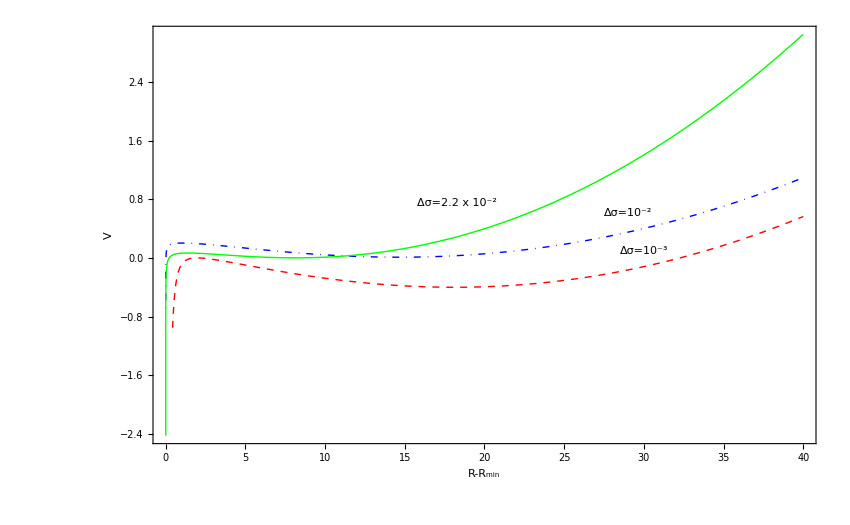

```mathematica
Clear[m1,m2,s1,b,ll,r1,rmin,vv];
m1=1;
m2=1.05;
rmin=3(m1+m2);
r=rmin+r1;
m1r=m1 - b r^2 +ll r^3 /6;
m2r=m2 - b r^2 +ll r^3 /6;
s0=(√15 √(-(m1-m2)^2/((3 (m1+m2)-r) r^3)))/(4 π)+s1;
msr= 4 Pi s0 r^2;
vv=1+(4 m1r m2r)/msr^2-(msr/(2 r) + (m1r+m2r)/(msr))^2;
s1=0.01;
ll=-0.01722;
b=-0.0397;
pla=Plot[vv,{r1,0,40},PlotStyle->{Blue,DotDashed,Thick},Frame->True,FrameLabel->{"R-R_min",V},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->20]];
FindMinimum[vv,{r1,5}]
14.636+3(m1+m2)

Clear[m1,m2,s1,b,ll,r1,rmin,vv];
m1=1;
m2=1.05;
rmin=3(m1+m2);
r=rmin+r1;
m1r=m1 - b r^2 +ll r^3 /6;
m2r=m2 - b r^2 +ll r^3 /6;
s0=(√15 √(-(m1-m2)^2/((3 (m1+m2)-r) r^3)))/(4 π)+s1;
msr= 4 Pi s0 r^2;
vv=1+(4 m1r m2r)/msr^2-(msr/(2 r) + (m1r+m2r)/(msr))^2;
s1=0.022;
ll=-0.06705;
b=-0.05182;
plb=Plot[vv,{r1,0,40},PlotStyle->{Green,Thick},Frame->True,FrameLabel->{"R",V}];
FindMinimum[vv,{r1,5}]
8.135 + 3(m1+m2)

figVr=Show[pla,plb,pltest,
Graphics[{Inset["Δσ=2.2 x 10^-2",{18.28,0.75}]}],
Graphics[{Inset["Δσ=10^-2",{29,0.61}]}],Graphics[{Inset["Δσ=10^-3",{30,0.1}]}],PlotRange->Automatic, BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->24],ImageSize->850]
```

```mathematica
Export["figure2.pdf",figVr,ImageResolution->1000,ImageSize->850]
```

```mathematica
Quit[]
```

#### Figure 3

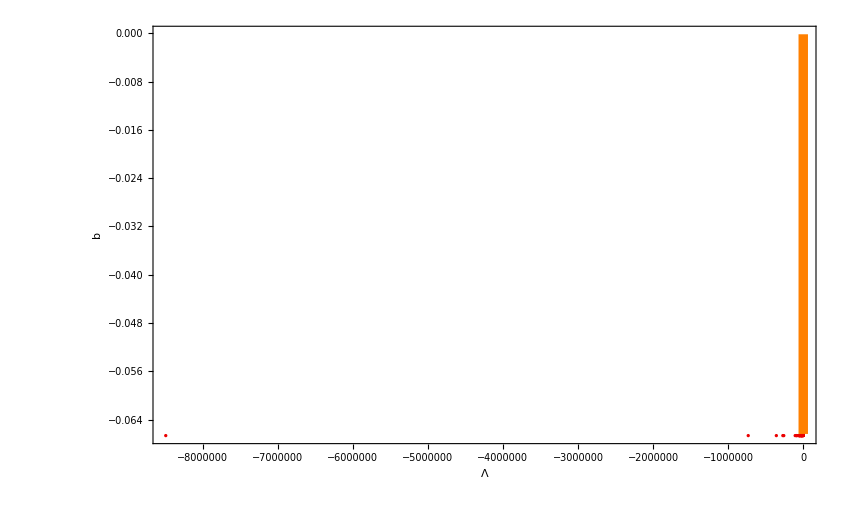

```mathematica
m1=1; (*Mass inside the shell*)
m2=1.5; (*Mass outside the shell*)

(*############################################################################################*)

lr[r_,ss_]:= -1/(16 π^2 r^6 ss^2)(3 m1^2-6 m1 m2+3 m2^2+48 m1 π^2 r^3 ss^2+48 m2 π^2 r^3 ss^2-48 π^2 r^4 ss^2+192 π^4 r^6 ss^4-6 (3 m1^2-6 m1 m2+3 m2^2+24 m1 π^2 r^3 ss^2+24 m2 π^2 r^3 ss^2-16 π^2 r^4 ss^2)); 
r0=3 m1+3 m2;(*Minimum value of r*)
s0[r_]:=(√15 √(-(m1-m2)^2/((3 m1+3 m2-r) r^3)))/(4π); (*Minimum value of σ, written as a function of r*)
br[r_,ss_]:= (3 m1^2-6 m1 m2+3 m2^2+24 m1 π^2 r^3 ss^2+24 m2 π^2 r^3 ss^2-16 π^2 r^4 ss^2)/(16 π^2 r^5 ss^2);

(*############################################################################################*)

pl1=ParametricPlot[{lr[r,s0[r]],br[r,s0[r]]},{r,r0,5000},Frame->True,FrameLabel->{b,Λ},PlotStyle->{Thickness[0.008],Orange}];
listrs={};
listbl={};
Do[
rRan=Random[Real,{r0,200}]; (*Real pseudo-random number in a range from the minimum value of r to 100 times that*)
sRan=Random[Real,{s0[rRan],1000s0[rRan]}];(*Real pseudo-random number in a range from the minimum value of σ, corresponding to the minimum value of r, to 100 times that*)
AppendTo[listrs,{rRan,sRan}];
AppendTo[listbl,{lr[rRan,sRan],br[rRan,sRan]}];,{i,1,50000}](*list with the values of the functions l and b for the above random values of σ and r, i.e the stability points*)
pl2=ListPlot[listbl,PlotStyle->Hue[0,1,0.92],FrameLabel->{Λ,b},Frame->True ,ImageSize->Large,PlotRange->{0,-0.08}];
fig1=Show[pl2,pl1,BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->24],ImageSize->850,PlotRange->{{0,-0.1},{0,-0.1}}]
```

```mathematica
Export["figure3.pdf",fig1,ImageResolution->1000,ImageSize->850]
```

```mathematica
Quit[]
```

### III.2. Stiff Matter fluid shell (w = 1)

#### Figure 4

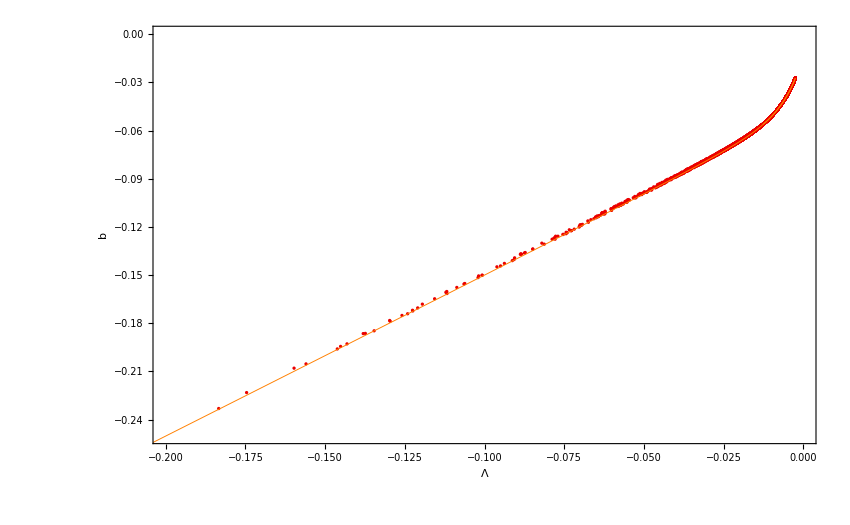

```mathematica
m1=1; (*Mass inside the shell*)
m2=1.5; (*Mass outside the shell*)

(*############################################################################################*)

lr[r_,ss_]:=-1/(16 π^2 r^8 ss^2)(3 m1^2 r^10-6 m1 m2 r^10+3 m2^2 r^10+48 m1 π^2 r^5 ss^2+48 m2 π^2 r^5 ss^2-48 π^2 r^6 ss^2+192 π^4 ss^4-6 (-m1^2 r^10+2 m1 m2 r^10-m2^2 r^10+24 m1 π^2 r^5 ss^2+24 m2 π^2 r^5 ss^2-16 π^2 r^6 ss^2+256 π^4 ss^4)); 
rmax=37/2 m2;(*Max value of r*)
r0=6m2;(*Min value of r*)
s0[r_]=(√(r^6))/(2 √37 π); (*Minimum value of σ, written as a function of r*)
smax[r_]:=(√(-6 m2 r^5+r^6))/(10 π);(*Max value of σ*)
br[r_,ss_]:=1/(16 π^2 r^7 ss^2)(-m1^2 r^10+2 m1 m2 r^10-m2^2 r^10+24 m1 π^2 r^5 ss^2+24 m2 π^2 r^5 ss^2-16 π^2 r^6 ss^2+256 π^4 ss^4);

(*############################################################################################*)


pl1=ParametricPlot[{lr[r,smax[r]],br[r,smax[r]]},{r,r0,rmax},Frame->True,FrameLabel->{b,Λ},PlotStyle->{Thickness[0.0008],Orange}];
pl2=ParametricPlot[{lr[r,s0[r]],br[r,s0[r]]},{r,r0,rmax},Frame->True,FrameLabel->{b,Λ},PlotStyle->{Thickness[0.0008],Orange}];
listrs={};
listbl={};
Do[
rRan=Random[Real,{r0,rmax}]; (*Real pseudo-random number in a range from the minimum value of r to 100 times that*)
sRan=Random[Real,{s0[rRan],smax[rRan]}];(*Real pseudo-random number in a range from the minimum value of σ, corresponding to the minimum value of r, to 100 times that*)
AppendTo[listrs,{rRan,sRan}];
AppendTo[listbl,{lr[rRan,sRan],br[rRan,sRan]}];,{i,1,50000}](*list with the values of the functions l and b for the above random values of σ and r, i.e the stability points*)

pl3=ListPlot[listbl,PlotStyle->Hue[0,1,0.92],FrameLabel->{Λ,b},Frame->True ,ImageSize->Large,PlotRange->{{-0.2,0},{-0.25,0}}];
pltot=Show[pl3,pl2,pl1,BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->24],ImageSize->850]
```

```mathematica
Export["figure4.pdf",pltot,ImageResolution->1000,ImageSize->850]
```

```mathematica
Quit[]
```

### III.3. Pressure-less Dust Fluid Shell (w = 0)

#### Figure 5

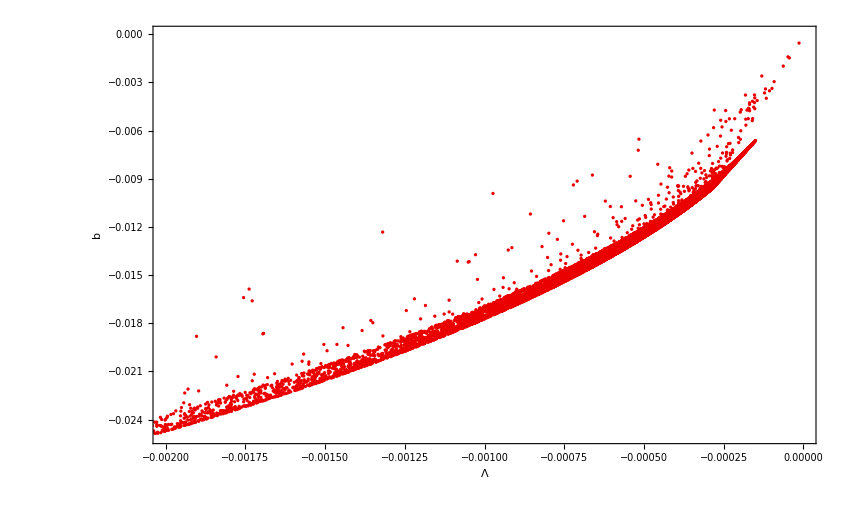

```mathematica
m1=1; (*Mass inside the shell*)
m2=1.5; (*Mass outside the shell*)

(*############################################################################################*)

lr[r_,ss_]:=-1/(16 π^2 r^4 ss^2)(3 m1^2 r^2-6 m1 m2 r^2+3 m2^2 r^2+48 m1 π^2 r ss^2+48 m2 π^2 r ss^2-48 π^2 r^2 ss^2+192 π^4 ss^4-6 (m1^2 r^2-2 m1 m2 r^2+m2^2 r^2+24 m1 π^2 r ss^2+24 m2 π^2 r ss^2-16 π^2 r^2 ss^2+128 π^4 ss^4)); 


br[r_,ss_]:=(m1^2 r^2-2 m1 m2 r^2+m2^2 r^2+24 m1 π^2 r ss^2+24 m2 π^2 r ss^2-16 π^2 r^2 ss^2+128 π^4 ss^4)/(16 π^2 r^3 ss^2);

(*############################################################################################*)


listrs={};
listbl={};
Do[
sRan=RandomReal[{0,100}]; (*Real pseudo-random number in a range from the minimum value of r to a number times that*)
rRan=RandomReal[{0,100}];(*Real pseudo-random number in a range from the minimum value of σ, corresponding to the minimum value of r, to a number times that*)
If[m2>0&&0<m1<m2&&sRan>(-m1+m2)/(4 π)&&rRan>-(24 (m1 π^2 sRan^2+m2 π^2 sRan^2))/(m1^2-2 m1 m2+m2^2-16 π^2 sRan^2)+8 √3 √((m1^2 π^4 sRan^4+10 m1 m2 π^4 sRan^4+m2^2 π^4 sRan^4+32 π^6 sRan^6)/((m1^2-2 m1 m2+m2^2-16 π^2 sRan^2)^2)),
{AppendTo[listrs,{rRan,sRan}];
AppendTo[listbl,{lr[rRan,sRan],br[rRan,sRan]}];},Continue[]],{i,1,500000}](*list with the values of the functions l and b for the above random values of σ and r, i.e the stability points*)
pl1=ListPlot[listbl,PlotStyle->Hue[0,1,0.92],FrameLabel->{Λ,b},Frame->True ,BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,FontFamily->"Times",FontSize->24],PlotRange->{{-0.002,0},{-0.025,0}},ImageSize->850]
```

```mathematica
Export["figure5.pdf",pl1,ImageResolution->1000,ImageSize->850]
```

```mathematica
Quit[]
```